```mathematica
k = 8.617*10^(-5); (*k_B in ev/K*)
B = 1/(k*T);
h = 4.135*10^-15; (* eV s*)
m = 5.109 * 10^5; (*eV/c^2*)
```

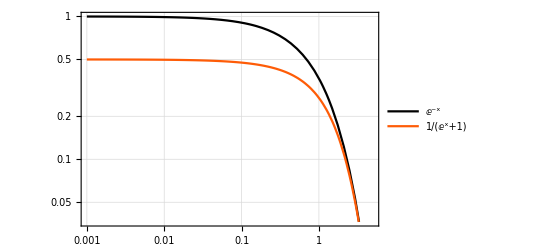

```mathematica
LogLogPlot[{E^-x,1/(E^x + 1)},{x,0.001,5},
PlotTheme->"Detailed", PlotStyle->ColorData[3,"ColorList"]]
```

```mathematica
ni[T_, Bgap_]:=2 (2 Pi k T  m (*eV^2 s^2/m^2*) / (3*10^10 *h (*eV cm*))^2 )^(3/2) * E^(- Bgap (*eV*)/(k*T*2) (*eV*))
```

```mathematica
ni[300,1.12]^2
```

9.58427×10^19

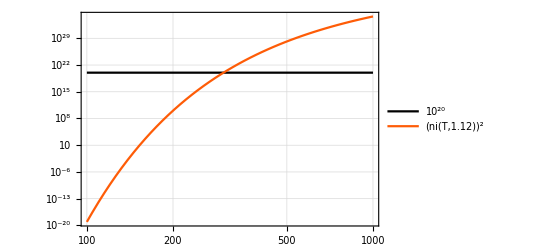

```mathematica
LogLogPlot[ {10^20,ni[T,1.12]^2},{T,100,1000},
PlotTheme->"Detailed", PlotStyle->ColorData[3,"ColorList"]]
```

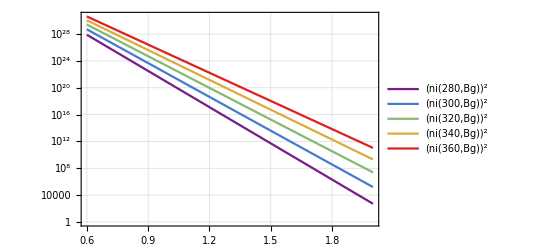

```mathematica
LogPlot[ {ni[280, Bg]^2, ni[300, Bg]^2, ni[320, Bg]^2, ni[340, Bg]^2, ni[360, Bg]^2},{Bg,0.6,2},
PlotTheme->"Detailed", PlotStyle->Thread@{Normal,ColorData["Rainbow"]/@Range[0,1,1/4]}]
```

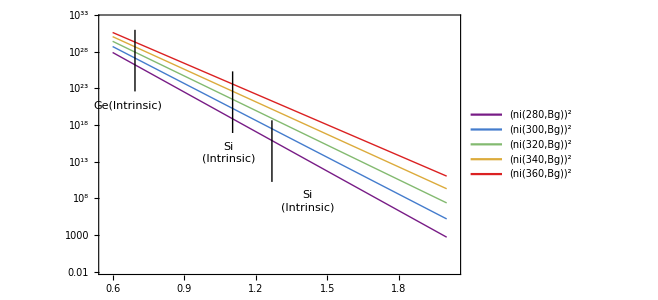

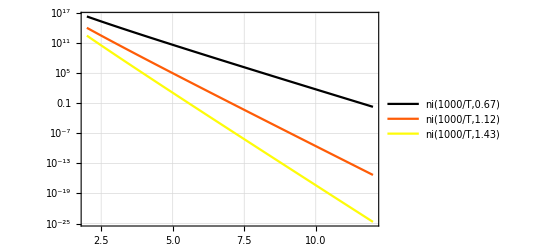

```mathematica
LogPlot[ {ni[1000/T, 0.67],ni[1000/T, 1.12], ni[1000/T, 1.43]},
{T,2,12},
PlotTheme->"Detailed", PlotStyle->ColorData[3,"ColorList"]]
```